# std::Math An implementation of standard math functions in Rust, rather than importing from a C library.

## pow(mantissa: float, exponent: float)

```mathematica
Series[Log[x],{x,0,10}]
```

Log[x]+O[x]^11

## sin(angle: float)

theta-theta^3/6+theta^5/120-theta^7/5040+theta^9/362880-theta^11/39916800+theta^13/6227020800-theta^15/1307674368000

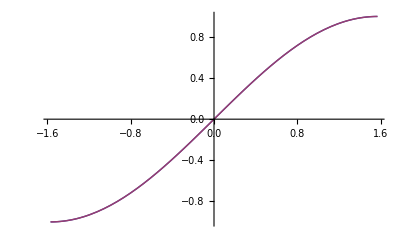

5.40412×10^-12

```mathematica
clear[f,theta,g];
sinApprox[theta_] = Normal[Series[Sin[theta],{theta,0,15}]]
Plot[{Sin[theta],sinApprox[theta]},{theta, -Pi/2,Pi/2}]
Evaluate[Abs[Sin[Pi/2-.01]-sinApprox[Pi/2-.01]]]
```

This Taylor Series is accurate in computing the sin of π/2 up to the 38th bit. This approximation is appropriate for 32-bit floating point integers.

## ln(x: float)

Piecewise[{{1/2 (-2+x)-1/8 (-2+x)^2+1/24 (-2+x)^3-1/64 (-2+x)^4+1/160 (-2+x)^5+Log[2], x>1}, {0.405465+0.666667 (-1.5+x)-0.222222 (-1.5+x)^2+0.0987654 (-1.5+x)^3-0.0493827 (-1.5+x)^4+0.0263374 (-1.5+x)^5-0.0146319 (-1.5+x)^6+0.00836109 (-1.5+x)^7-0.00487731 (-1.5+x)^8, 0.5<x≤1}, {0.223943+0.799361 (-1.251+x)-0.319489 (-1.251+x)^2+0.170258 (-1.251+x)^3-0.102073 (-1.251+x)^4+0.0652745 (-1.251+x)^5-0.0434815 (-1.251+x)^6+0.0297921 (-1.251+x)^7-0.0208378 (-1.251+x)^8+0.0148061 (-1.251+x)^9-0.0106519 (-1.251+x)^10+0.00774064 (-1.251+x)^11-0.00567193 (-1.251+x)^12, 0.25<x≤0.5}, {0.00995033+0.990099 (-1.01+x)-0.490148 (-1.01+x)^2+0.32353 (-1.01+x)^3-0.240245 (-1.01+x)^4+0.190293 (-1.01+x)^5-0.157008 (-1.01+x)^6+0.133245 (-1.01+x)^7-0.115435 (-1.01+x)^8+0.101593 (-1.01+x)^9-0.0905287 (-1.01+x)^10+0.081484 (-1.01+x)^11-0.0739541 (-1.01+x)^12+0.0675894 (-1.01+x)^13-0.0621402 (-1.01+x)^14+0.0574233 (-1.01+x)^15-0.0533013 (-1.01+x)^16, 0<x≤0.25}, {0, True}}]

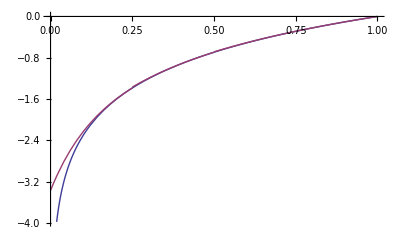

```mathematica
clear[lnApprox];
lnApprox[x_]=Piecewise[{{Normal[Series[Log[x+1],{x,1,5}]]/.x->x-1,x>1},{Normal[Series[Log[x+1],{x,.5,8}]]/.x->x-1,0.5<x≤1},
{Normal[Series[Log[x+1],{x,0.251,12}]]/.x->x-1,0.25<x≤0.5},
{Normal[Series[Log[x+1],{x,0.01,16}]]/.x->x-1,0<x≤0.25}}]
Plot[{Log[x],lnApprox[x]},{x,0,1}]
```